```mathematica
<<KurukuruW`
```

```mathematica
CircularWrap /@ {1,{1},{{Pi}}, {- Pi,2 Pi, 3 Pi, 3.1 Pi}}
```

{1,{1},{{π}},{π,0,π,-2.82743}}

```mathematica
CircularWrap[0.4 + 7 Pi - (0.4 - Pi)] < 0.00001
```

True

```mathematica
CircularMinus[{2, 2, 3Pi, 3Pi}, {1, 6, 5Pi,11/2 Pi}]
```

{1,-4+2 π,0,-π/2}

```mathematica
CircularAccumulate[
Join[
Table[n/3 Pi,{n,0,30}],
Table[10 Pi-n/3 Pi,{n,0,30}]
]
]
```

{0,π/3,(2 π)/3,π,(4 π)/3,(5 π)/3,2 π,(7 π)/3,(8 π)/3,3 π,(10 π)/3,(11 π)/3,4 π,(13 π)/3,(14 π)/3,5 π,(16 π)/3,(17 π)/3,6 π,(19 π)/3,(20 π)/3,7 π,(22 π)/3,(23 π)/3,8 π,(25 π)/3,(26 π)/3,9 π,(28 π)/3,(29 π)/3,10 π,10 π,(29 π)/3,(28 π)/3,9 π,(26 π)/3,(25 π)/3,8 π,(23 π)/3,(22 π)/3,7 π,(20 π)/3,(19 π)/3,6 π,(17 π)/3,(16 π)/3,5 π,(14 π)/3,(13 π)/3,4 π,(11 π)/3,(10 π)/3,3 π,(8 π)/3,(7 π)/3,2 π,(5 π)/3,(4 π)/3,π,(2 π)/3,π/3,0}

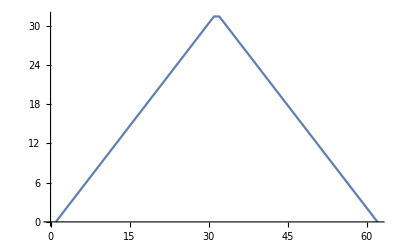

```mathematica
ListLinePlot[%]
```